# Graphical calculus §2.1.3: pivotal categories

## Turaev & Virelizier, Monoidal Categories and Topological Field Theory, pp. 33–35 · continues graphical-calculus-2.1-simplify.nb

## 0. Setup

This notebook builds on the engine of graphical-calculus-2.1-simplify.nb: the StringDiagram data model, the layered form LD, level exchange (Figure 2.1), the rewrite rules and simplifyTrace. The first cell loads that notebook's code cells, so both notebooks must sit in the same folder (Desktop/Research/Monoidal Graphical Calculus).

```mathematica
ClearAll["Global`*"];
(* the §2.1.1–2.1.2 engine: renderer, layered form, level exchange, rules, simplifyTrace, ... *)
engineNotebook = FileNameJoin[{$HomeDirectory, "Desktop", "Research", "Monoidal Graphical Calculus", "graphical-calculus-2.1-simplify.nb"}];
(* With (not Module): that notebook starts with ClearAll["Global`*"], which would otherwise clear the loader's own variables *)
With[{cells = Cases[Get[engineNotebook], Cell[c_, "Input" | "Code", ___] :> c, Infinity], name = FileNameTake[engineNotebook]},
 Scan[Quiet@Check[TimeConstrained[ToExpression[#, StandardForm]; Null, 120], Null] &, cells];
 Print["Loaded ", Length[cells], " code cells from ", name]];
```

## 1. Oriented arcs

In a pivotal category every arc carries an orientation. As in the book, diagrams read from bottom to top. An arc coloured X that points down contributes X to the source or target; an arc coloured X that points up contributes the dual X*. In the data the second case is simply the colour "X*", and the renderer draws it as an X arc with an upward arrow. Since an arc can be turned round, X** = X.

The four duality morphisms of §1.7.1 are ev_X : X* ⊗ X → 𝟙 and ẽv_X : X ⊗ X* → 𝟙 (the caps), and coev_X : 𝟙 → X ⊗ X* and c̃oev_X : 𝟙 → X* ⊗ X (the cups). In the data, ẽv and c̃oev are written "ev~" and "coev~". The pair (ẽv_X, c̃oev_X) is a non-degenerate pairing with its inverse, just like (ev_X, coev_X).

```mathematica
(* ===== Oriented arcs: the colour X (arrow down) and the colour X* (arrow up) ===== *)
starQ[c_String] := StringEndsQ[c, "*"];
starQ[_] := False;
baseC[c_String] := StringTrim[c, "*" ..];
dualC[c_String] := If[starQ[c], StringDrop[c, -1], c <> "*"];   (* X** = X: the arc just turns round *)
dualRow[cs_List] := Reverse[dualC /@ cs];                          (* (X ⊗ Y)* = Y* ⊗ X* *)
starName[s_String] := If[StringEndsQ[s, "*"], StringDrop[s, -1], s <> "*"];  (* f ↦ f*, f* ↦ f *)

(* the four duality morphisms of §2.1.3 *)
evP[x_] := B[Subscript["ev", x], {dualC[x], x}, {}];          (* ev_X : X* ⊗ X → 𝟙 *)
evtP[x_] := B[Subscript["ev~", x], {x, dualC[x]}, {}];        (* ẽv_X : X ⊗ X* → 𝟙 *)
coevP[x_] := B[Subscript["coev", x], {}, {x, dualC[x]}];      (* coev_X : 𝟙 → X ⊗ X* *)
coevtP[x_] := B[Subscript["coev~", x], {}, {dualC[x], x}];    (* c̃oev_X : 𝟙 → X* ⊗ X *)
capCupQ[s_] := MatchQ[s, Subscript["ev" | "ev~" | "coev" | "coev~", _]];

(* ẽv_X and c̃oev_X form a second pairing and its inverse, so the (2.1) zigzags apply to them too *)
pairQ[Subscript["ev~", x_], Subscript["coev~", x_]] := True;

(* typesetting: X* as X with a superscript star, ẽv and c̃oev with tildes *)
dispSym[s_String] /; starQ[s] && StringLength[s] > 1 := Superscript[dispSym[StringDrop[s, -1]], Style["*", Plain]];
dispSym[Subscript["ev~", b_]] := Subscript[Style["e\:0303v", Plain], dispSym[b]];
dispSym[Subscript["coev~", b_]] := Subscript[Style["c\:0303oev", Plain], dispSym[b]];
```

## 2. Caps, cups and arrows

The renderer of §2.1.2 is redefined so that every arc has an arrow and the four duality morphisms are drawn as caps and cups instead of boxes. Everything else (layout, labels, show, showEq, showTrace) is unchanged.

```mathematica
(* ===== Renderer for §2.1.3: every arc carries an arrow, and ev, ẽv, coev, c̃oev are caps and cups =====
   As in the book, diagrams read from bottom to top. An arc coloured X points down and contributes X;
   an arc coloured X* is drawn as an arc coloured X pointing up. *)
arrowHead[{x_, y_}, up_] := With[{s = If[up, 1, -1]},
   Polygon[{{x - 0.07, y - 0.06 s}, {x + 0.07, y - 0.06 s}, {x, y + 0.07 s}}]];
render[d : StringDiagram[bs_, ws_]] := Module[{caps, plain, lines, boxes, arcs, pts, xr, yr, attached},
   caps = Select[bs, capCupQ[#[[2]]] &];
   plain = Complement[bs, caps];
   attached[n_, edge_] := Sort[#[[2]] & /@ Select[ws, MemberQ[{#[[3]], #[[4]]}, edge[n]] &]];
   lines = Table[With[{x = w[[2]], y1 = endY[d, w[[3]]], y2 = endY[d, w[[4]]], left = Length[w] > 4, c = w[[1]]},
      {Black, AbsoluteThickness[2.4], Line[{{x, y1}, {x, y2}}],
       If[c === unit, {}, arrowHead[{x, (y1 + y2)/2}, starQ[c]]],
       Text[Style[dispSym[If[StringQ[c], baseC[c], c]], 12, FontFamily -> "Times"],
        {x + If[left, -0.1, 0.1], labelY[w, y1, y2]}, {If[left, 1, -1], 0}]}], {w, ws}];
   arcs = Table[With[{xs = If[MatchQ[b[[2]], Subscript["ev" | "ev~", _]], attached[b[[1]], BottomEdge], attached[b[[1]], TopEdge]],
       cap = MatchQ[b[[2]], Subscript["ev" | "ev~", _]]},
      If[Length[xs] =!= 2, {},
       {Black, AbsoluteThickness[2.4],
        Circle[{Mean[xs], If[cap, b[[4]] - hgt/2, b[[4]] + hgt/2]}, {(xs[[2]] - xs[[1]])/2, hgt},
         If[cap, {0, Pi}, {Pi, 2 Pi}]]}]], {b, caps}];
   boxes = Table[{EdgeForm[{Black, AbsoluteThickness[1.2]}], White,
      Rectangle[{b[[3, 1]], b[[4]] - hgt/2}, {b[[3, 2]], b[[4]] + hgt/2}], Black,
      Text[Style[dispSym[b[[2]]], If[Head[b[[2]]] === Subscript, 13, 15], FontFamily -> "Times"],
       {Mean[b[[3]]], b[[4]]}]}, {b, plain}];
   pts = Join[Flatten[Table[{{w[[2]], endY[d, w[[3]]]}, {w[[2]], endY[d, w[[4]]]}}, {w, ws}], 1],
     Flatten[Table[{{b[[3, 1]], b[[4]] - hgt}, {b[[3, 2]], b[[4]] + hgt}}, {b, bs}], 1]];
   {xr, yr} = CoordinateBounds[pts];
   yr = {Min[yr[[1]], -1], Max[yr[[2]], 1]};
   Graphics[{lines, arcs, boxes}, PlotRange -> {xr + {-0.45, 0.45}, yr + {-0.1, 0.1}},
    ImageSize -> 62 (xr[[2]] - xr[[1]] + 0.9), BaselinePosition -> Axis]];
```

Page 34 of the book: the caps ev_X and ẽv_X, the cups coev_X and c̃oev_X, id_{X*} as an upward X arc, and a box f : X* ⊗ Y → U ⊗ V* ⊗ W.

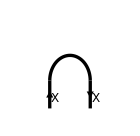
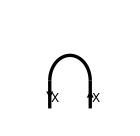
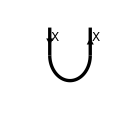
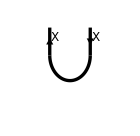
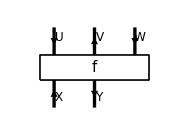
-Graphics-
ev_X      -Graphics-
(ẽv)_X      -Graphics-
coev_X      -Graphics-
(c̃oev)_X
-Graphics- | id_(X^*) | X^*  →  X^*        -Graphics- | f | X^*⊗Y  →  U⊗V^*⊗W

```mathematica
boxP[B[s_, i_, o_]] := LD[i, {{0, B[s, i, o]}}];
Column[{
  Row[Riffle[Column[{render[fromLayered[boxP[#]]], Style[pretty[sym[#]], 14, FontFamily -> "Times"]}, Alignment -> Center] & /@
     {evP["X"], evtP["X"], coevP["X"], coevtP["X"]}, "      "]],
  Row[{show[fromLayered[idL[{"X*"}]]], "        ", show[fromLayered[boxP[B["f", {"X*", "Y"}, {"U", "V*", "W"}]]]]}]}, Spacings -> 2]
```

## 3. Rules for §2.1.3

The duality identities (1.12) and (1.13), drawn in Figure 2.2, are zigzags of the pairings ev/coev and ẽv/c̃oev, so the (2.1) rules snakeL and snakeR already prove them once pairQ knows that ẽv_X and c̃oev_X are paired. New rules: the two expressions for the dual morphism f* : Y* → X* (Figure 2.3), read right to left as folds, and the four dual morphism identities (Figure 2.4), read as slides that replace f* by f.

```mathematica
(* ===== Rules for §2.1.3 =====
   The duality identities (1.12) and (1.13) of Figure 2.2 are zigzags of the pairings ev/coev and ẽv/c̃oev,
   so snakeL and snakeR from §2.1.2 already cover them. New here: the two expressions for f* (Figure 2.3)
   and the four dual morphism identities (Figure 2.4). *)
dualBoxQ[s_] := StringQ[s] && StringEndsQ[s, "*"] && StringLength[s] > 1;

(* Figure 2.3, left: f* = (ev_Y ⊗ id_X* )(id_Y* ⊗ f ⊗ id_X* )(id_Y* ⊗ coev_X) *)
foldStarL[{a_, B[Subscript["coev", x_], {}, {x_, dx_}]}, {a2_, B[f_String, {x_}, {y_}]},
    {a3_, B[Subscript["ev", y_], {dy_, y_}, {}]}] /; a2 == a && a3 == a - 1 && f =!= unit := {{a - 1, B[starName[f], {dy}, {dx}]}};
foldStarL[__] := $Failed;
(* Figure 2.3, right: f* = (id_X* ⊗ ẽv_Y)(id_X* ⊗ f ⊗ id_Y* )(c̃oev_X ⊗ id_Y* ) *)
foldStarR[{a_, B[Subscript["coev~", x_], {}, {dx_, x_}]}, {a2_, B[f_String, {x_}, {y_}]},
    {a3_, B[Subscript["ev~", y_], {y_, dy_}, {}]}] /; a2 == a + 1 && a3 == a + 1 := {{a, B[starName[f], {dy}, {dx}]}};
foldStarR[__] := $Failed;

(* Figure 2.4, first line (special cases of (2.2)) *)
slideEvP[{a_, B[s_?dualBoxQ, {dy_}, {dx_}]}, {b_, B[Subscript["ev", x_], {dx_, x_}, {}]}] /; b == a :=
  {{a + 1, B[starName[s], {x}, {dualC[dy]}]}, {a, B[Subscript["ev", dualC[dy]], {dy, dualC[dy]}, {}]}};
slideEvP[__] := $Failed;
slideCoevP[{a_, B[Subscript["coev", y_], {}, {y_, dy_}]}, {b_, B[s_?dualBoxQ, {dy_}, {dx_}]}] /; b == a + 1 :=
  {{a, B[Subscript["coev", dualC[dx]], {}, {dualC[dx], dx}]}, {a, B[starName[s], {dualC[dx]}, {y}]}};
slideCoevP[__] := $Failed;
(* Figure 2.4, second line: ẽv_X(id_X ⊗ f* ) = ẽv_Y(f ⊗ id_Y* ),  (f* ⊗ id_Y)c̃oev_Y = (id_X* ⊗ f)c̃oev_X *)
slideEvtP[{a_, B[s_?dualBoxQ, {dy_}, {dx_}]}, {b_, B[Subscript["ev~", x_], {x_, dx_}, {}]}] /; b == a - 1 :=
  {{b, B[starName[s], {x}, {dualC[dy]}]}, {b, B[Subscript["ev~", dualC[dy]], {dualC[dy], dy}, {}]}};
slideEvtP[__] := $Failed;
slideCoevtP[{a_, B[Subscript["coev~", y_], {}, {dy_, y_}]}, {b_, B[s_?dualBoxQ, {dy_}, {dx_}]}] /; b == a :=
  {{a, B[Subscript["coev~", dualC[dx]], {}, {dx, dualC[dx]}]}, {a + 1, B[starName[s], {dualC[dx]}, {y}]}};
slideCoevtP[__] := $Failed;

(* the pivotal rule set: the §2.1.2 rules with ∨ replaced by * and the right-hand duality added *)
rulesP = <|
   "unit strands" -> rules["unit strands"],
   "\[CircleTimes]-coloured strands" -> rules["\[CircleTimes]-coloured strands"],
   "(2.1) left zigzag" -> rules["(2.1) left zigzag"],
   "(2.1) right zigzag" -> rules["(2.1) right zigzag"],
   "Figure 2.3: f* via ev, coev" -> {3, foldStarL},
   "Figure 2.3: f* via e\:0303v, c\:0303oev" -> {3, foldStarR},
   "Figure 2.4: slide through ev" -> {2, slideEvP},
   "Figure 2.4: slide through coev" -> {2, slideCoevP},
   "Figure 2.4: slide through e\:0303v" -> {2, slideEvtP},
   "Figure 2.4: slide through c\:0303oev" -> {2, slideCoevtP}|>;
rulesPRightFirst = Join[KeyTake[rulesP, {"(2.1) right zigzag"}], rulesP];
```

## 4. The pictures of §2.1.3 as layered diagrams

```mathematica
(* ===== The pictures of §2.1.3, built as layered diagrams ===== *)
boxP[B[s_, i_, o_]] := LD[i, {{0, B[s, i, o]}}];
fB = B["f", {"X"}, {"Y"}];
(* f* : Y* → X* and its two expressions (Figure 2.3) *)
fStar = boxP[B["f*", {"Y*"}, {"X*"}]];
fStarL = stackL[stackL[besideL[idL[{"Y*"}], boxP[coevP["X"]]], besideL[besideL[idL[{"Y*"}], boxP[fB]], idL[{"X*"}]]],
   besideL[boxP[evP["Y"]], idL[{"X*"}]]];
fStarR = stackL[stackL[besideL[boxP[coevtP["X"]], idL[{"Y*"}]], besideL[besideL[idL[{"X*"}], boxP[fB]], idL[{"Y*"}]]],
   besideL[idL[{"X*"}], boxP[evtP["Y"]]]];
(* Figure 2.2: the duality identities (1.12) and (1.13) *)
z1 = stackL[besideL[boxP[coevP["X"]], idL[{"X"}]], besideL[idL[{"X"}], boxP[evP["X"]]]];      (* (id_X ⊗ ev_X)(coev_X ⊗ id_X) *)
z2 = stackL[besideL[idL[{"X"}], boxP[coevtP["X"]]], besideL[boxP[evtP["X"]], idL[{"X"}]]];    (* (ẽv_X ⊗ id_X)(id_X ⊗ c̃oev_X) *)
z3 = stackL[besideL[idL[{"X*"}], boxP[coevP["X"]]], besideL[boxP[evP["X"]], idL[{"X*"}]]];    (* (ev_X ⊗ id_X* )(id_X* ⊗ coev_X) *)
z4 = stackL[besideL[boxP[coevtP["X"]], idL[{"X*"}]], besideL[idL[{"X*"}], boxP[evtP["X"]]]];  (* (id_X* ⊗ ẽv_X)(c̃oev_X ⊗ id_X* ) *)
(* Figure 2.4: the dual morphism identities *)
fS = B["f*", {"Y*"}, {"X*"}];
d1L = stackL[besideL[boxP[fS], idL[{"X"}]], boxP[evP["X"]]];          (* ev_X(f* ⊗ id_X) *)
d1R = stackL[besideL[idL[{"Y*"}], boxP[fB]], boxP[evP["Y"]]];         (* ev_Y(id_Y* ⊗ f) *)
d2L = stackL[boxP[coevP["Y"]], besideL[idL[{"Y"}], boxP[fS]]];        (* (id_Y ⊗ f* )coev_Y *)
d2R = stackL[boxP[coevP["X"]], besideL[boxP[fB], idL[{"X*"}]]];       (* (f ⊗ id_X* )coev_X *)
d3L = stackL[besideL[idL[{"X"}], boxP[fS]], boxP[evtP["X"]]];         (* ẽv_X(id_X ⊗ f* ) *)
d3R = stackL[besideL[boxP[fB], idL[{"Y*"}]], boxP[evtP["Y"]]];        (* ẽv_Y(f ⊗ id_Y* ) *)
d4L = stackL[boxP[coevtP["Y"]], besideL[boxP[fS], idL[{"Y"}]]];       (* (f* ⊗ id_Y)c̃oev_Y *)
d4R = stackL[boxP[coevtP["X"]], besideL[idL[{"X*"}], boxP[fB]]];      (* (id_X* ⊗ f)c̃oev_X *)
(* a box with mixed orientations: f : X* ⊗ Y → U ⊗ V* ⊗ W *)
mixed = boxP[B["f", {"X*", "Y"}, {"U", "V*", "W"}]];
```

## 5. Figure 2.2: the duality identities

(id_X ⊗ ev_X)(coev_X ⊗ id_X) = id_X = (ẽv_X ⊗ id_X)(id_X ⊗ c̃oev_X)   (1.12)
(ev_X ⊗ id_{X*})(id_{X*} ⊗ coev_X) = id_{X*} = (id_{X*} ⊗ ẽv_X)(c̃oev_X ⊗ id_{X*})   (1.13)

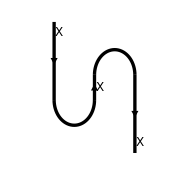
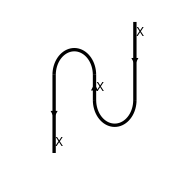
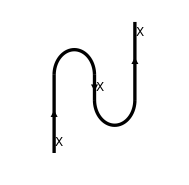
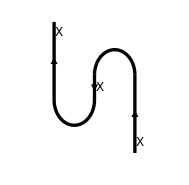
-Graphics-  =  -Graphics-  =  -Graphics-
(id_X⊗ev_X)∘(coev_X⊗id_X)   =   id_X   =   ((ẽv)_X⊗id_X)∘(id_X⊗(c̃oev)_X)
-Graphics-  =  -Graphics-  =  -Graphics-
(ev_X⊗id_(X^*))∘(id_(X^*)⊗coev_X)   =   id_(X^*)   =   (id_(X^*)⊗(ẽv)_X)∘((c̃oev)_X⊗id_(X^*))

```mathematica
Column[{showEq[fromLayered /@ {z1, idL[{"X"}], z2}], showEq[fromLayered /@ {z3, idL[{"X*"}], z4}]}, Spacings -> 3]
```

```mathematica
Column[showTrace[simplifyTrace[#, rulesP]] & /@ {z1, z2, z3, z4}, Spacings -> 3]
```

-Graphics-(2.1) left zigzag
⟶-Graphics-
(id_X⊗ev_X)∘(coev_X⊗id_X)   ⟶   id_X
    -Graphics-(2.1) right zigzag
⟶-Graphics-
((ẽv)_X⊗id_X)∘(id_X⊗(c̃oev)_X)   ⟶   id_X
    -Graphics-(2.1) right zigzag
⟶-Graphics-
(ev_X⊗id_(X^*))∘(id_(X^*)⊗coev_X)   ⟶   id_(X^*)
    -Graphics-(2.1) left zigzag
⟶-Graphics-
(id_(X^*)⊗(ẽv)_X)∘((c̃oev)_X⊗id_(X^*))   ⟶   id_(X^*)

## 6. Figure 2.3: two expressions for the dual morphism

f* = (ev_Y ⊗ id_{X*})(id_{Y*} ⊗ f ⊗ id_{X*})(id_{Y*} ⊗ coev_X) = (id_{X*} ⊗ ẽv_Y)(id_{X*} ⊗ f ⊗ id_{Y*})(c̃oev_X ⊗ id_{Y*}). The equality of these two expressions is condition (i) of §1.7.1: it is what makes the category pivotal.

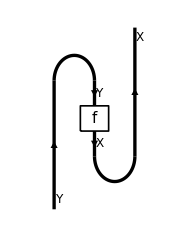
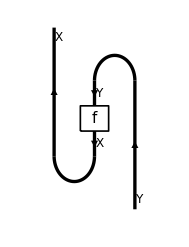
-Graphics-  =  -Graphics-  =  -Graphics-
f^*   =   (ev_Y⊗id_(X^*))∘(id_(Y^*)⊗f⊗id_(X^*))∘(id_(Y^*)⊗coev_X)   =   (id_(X^*)⊗(ẽv)_Y)∘(id_(X^*)⊗f⊗id_(Y^*))∘((c̃oev)_X⊗id_(Y^*))

```mathematica
showEq[fromLayered /@ {fStar, fStarL, fStarR}]
```

```mathematica
Column[{showTrace[simplifyTrace[fStarL, rulesP]], showTrace[simplifyTrace[fStarR, rulesP]]}, Spacings -> 3]
```

-Graphics-Figure 2.3: f* via ev, coev
⟶-Graphics-
(ev_Y⊗id_(X^*))∘(id_(Y^*)⊗f⊗id_(X^*))∘(id_(Y^*)⊗coev_X)   ⟶   f^*
    -Graphics-Figure 2.3: f* via ẽv, c̃oev
⟶-Graphics-
(id_(X^*)⊗(ẽv)_Y)∘(id_(X^*)⊗f⊗id_(Y^*))∘((c̃oev)_X⊗id_(Y^*))   ⟶   f^*

## 7. Figure 2.4: the dual morphism identities

ev_X(f* ⊗ id_X) = ev_Y(id_{Y*} ⊗ f),   (id_Y ⊗ f*)coev_Y = (f ⊗ id_{X*})coev_X,
ẽv_X(id_X ⊗ f*) = ẽv_Y(f ⊗ id_{Y*}),   (f* ⊗ id_Y)c̃oev_Y = (id_{X*} ⊗ f)c̃oev_X.
The first line is (2.2) with ∨ replaced by *.

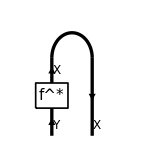
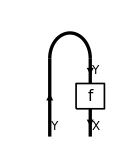
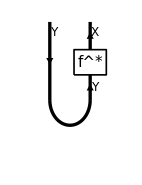
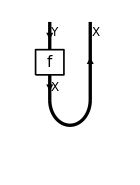
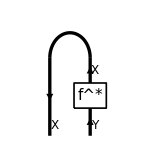
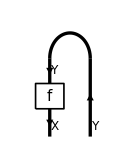
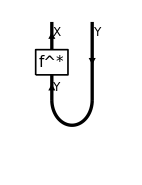
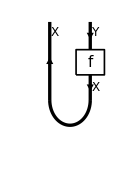
-Graphics-  =  -Graphics-
ev_X∘(f^*⊗id_X)   =   ev_Y∘(id_(Y^*)⊗f)
-Graphics-  =  -Graphics-
(id_Y⊗f^*)∘coev_Y   =   (f⊗id_(X^*))∘coev_X
-Graphics-  =  -Graphics-
(ẽv)_X∘(id_X⊗f^*)   =   (ẽv)_Y∘(f⊗id_(Y^*))
-Graphics-  =  -Graphics-
(f^*⊗id_Y)∘(c̃oev)_Y   =   (id_(X^*)⊗f)∘(c̃oev)_X

```mathematica
Column[showEq[fromLayered /@ #] & /@ {{d1L, d1R}, {d2L, d2R}, {d3L, d3R}, {d4L, d4R}}, Spacings -> 3]
```

```mathematica
Column[showTrace[simplifyTrace[#, rulesP]] & /@ {d1L, d2L, d3L, d4L}, Spacings -> 3]
```

-Graphics-Figure 2.4: slide through ev
⟶-Graphics-
ev_X∘(f^*⊗id_X)   ⟶   ev_Y∘(id_(Y^*)⊗f)
    -Graphics-Figure 2.4: slide through coev
⟶-Graphics-
(id_Y⊗f^*)∘coev_Y   ⟶   (f⊗id_(X^*))∘coev_X
    -Graphics-Figure 2.4: slide through ẽv
⟶-Graphics-
(ẽv)_X∘(id_X⊗f^*)   ⟶   (ẽv)_Y∘(f⊗id_(Y^*))
    -Graphics-Figure 2.4: slide through c̃oev
⟶-Graphics-
(f^*⊗id_Y)∘(c̃oev)_Y   ⟶   (id_(X^*)⊗f)∘(c̃oev)_X

## 8. Exercise 2.1.5

Let ω : X ⊗ Y → 𝟙 be a non-degenerate pairing with inverse Ω : 𝟙 → Y ⊗ X. The map φ : End(X) → End(Y), f ↦ (id_Y ⊗ ω)(id_Y ⊗ f ⊗ id_Y)(Ω ⊗ id_Y), is an anti-isomorphism of monoids with inverse ψ : g ↦ (ω ⊗ id_X)(id_X ⊗ g ⊗ id_X)(id_X ⊗ Ω). The rules prove ψ(φ(f)) = f, φ(ψ(g)) = g and φ(hf) = φ(f)φ(h).

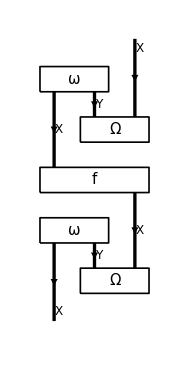
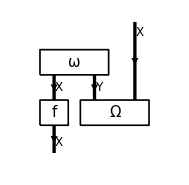
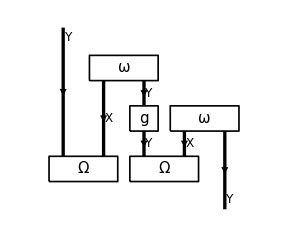
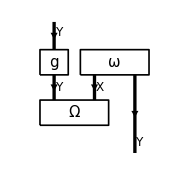
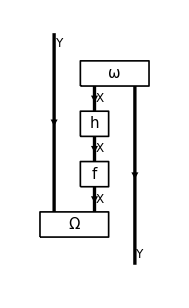
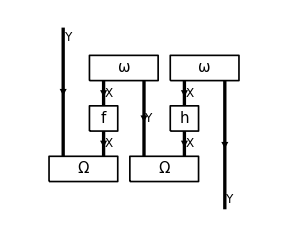
-Graphics-(2.1) right zigzag
⟶-Graphics-(2.1) right zigzag
⟶-Graphics-
(ω⊗id_X)∘(id_X⊗Ω)∘f∘(ω⊗id_X)∘(id_X⊗Ω)   ⟶   (ω⊗id_X)∘(f⊗Ω)   ⟶   f
    -Graphics-(2.1) left zigzag
⟶-Graphics-(2.1) left zigzag
⟶-Graphics-
(id_Y⊗ω)∘(id_Y⊗id_X⊗g⊗ω)∘(Ω⊗Ω⊗id_Y)   ⟶   (g⊗ω)∘(Ω⊗id_Y)   ⟶   g
-Graphics-  =  -Graphics-
(id_Y⊗ω)∘(id_Y⊗h⊗id_Y)∘(id_Y⊗f⊗id_Y)∘(Ω⊗id_Y)   =   (id_Y⊗ω⊗ω)∘(id_Y⊗f⊗id_Y⊗h⊗id_Y)∘(Ω⊗Ω⊗id_Y)

```mathematica
phi[fl_LD] := stackL[stackL[besideL[boxL["\[CapitalOmega]", {}, {"Y", "X"}], idL[{"Y"}]], besideL[besideL[idL[{"Y"}], fl], idL[{"Y"}]]],
   besideL[idL[{"Y"}], boxL["\[Omega]", {"X", "Y"}, {}]]];
psi[gl_LD] := stackL[stackL[besideL[idL[{"X"}], boxL["\[CapitalOmega]", {}, {"Y", "X"}]], besideL[besideL[idL[{"X"}], gl], idL[{"X"}]]],
   besideL[boxL["\[Omega]", {"X", "Y"}, {}], idL[{"X"}]]];
fE = boxL["f", {"X"}, {"X"}]; hE = boxL["h", {"X"}, {"X"}]; gE = boxL["g", {"Y"}, {"Y"}];
Column[{showTrace[simplifyTrace[psi[phi[fE]], rulesP]], showTrace[simplifyTrace[phi[psi[gE]], rulesP]],
  showEq[fromLayered /@ {phi[stackL[fE, hE]], stackL[phi[hE], phi[fE]]}]}, Spacings -> 3]
```

## 9. Tests

Every identity is checked twice: by the rules (sameQ) and in vector spaces, where X* is the dual space, ev and ẽv are the pairing, coev and c̃oev are Σ e_i ⊗ e_i*, and f* is the transpose of f.

```mathematica
SeedRandom[7];
fMP = RandomInteger[{-3, 3}, {3, 2}];
dimsP = <|"X" -> 2, "Y" -> 3, "X*" -> 2, "Y*" -> 3|>;
matsP = <|"f" -> fMP, "f*" -> Transpose[fMP],
   Subscript["ev", "X"] -> {vec[2]}, Subscript["ev", "Y"] -> {vec[3]}, Subscript["ev~", "X"] -> {vec[2]}, Subscript["ev~", "Y"] -> {vec[3]},
   Subscript["coev", "X"] -> Transpose[{vec[2]}], Subscript["coev", "Y"] -> Transpose[{vec[3]}],
   Subscript["coev~", "X"] -> Transpose[{vec[2]}], Subscript["coev~", "Y"] -> Transpose[{vec[3]}]|>;
mat[ld_] := toMatrix[toExpression[fromLayered[ld]], dimsP, matsP];
diagsP = {fStarL, fStarR, z1, z2, z3, z4, d1L, d1R, d2L, d2R, d3L, d3R, d4L, d4R};
<|
 "Figure 2.2: the four zigzags reduce to identities" -> (simplifyLD[#, rulesP] & /@ {z1, z2, z3, z4} === {idL[{"X"}], idL[{"X"}], idL[{"X*"}], idL[{"X*"}]}),
 "Figure 2.2 in matrices" -> (mat /@ {z1, z2, z3, z4} === ConstantArray[IdentityMatrix[2], 4]),
 "Figure 2.3: both expressions fold to f*" -> (simplifyLD[fStarL, rulesP] === simplifyLD[fStarR, rulesP] === fStar),
 "Figure 2.3 in matrices" -> (mat[fStarL] === mat[fStarR] === Transpose[fMP]),
 "Figure 2.4 by the rules" -> (sameQ[d1L, d1R, rulesP] && sameQ[d2L, d2R, rulesP] && sameQ[d3L, d3R, rulesP] && sameQ[d4L, d4R, rulesP]),
 "Figure 2.4 in matrices" -> (mat[d1L] === mat[d1R] && mat[d2L] === mat[d2R] && mat[d3L] === mat[d3R] && mat[d4L] === mat[d4R]),
 "every step keeps the matrix" -> And @@ (Equal @@ (mat /@ (simplifyTrace[#, rulesP][[All, 2]])) & /@ diagsP),
 "every layered form is valid" -> And @@ (validQ[simplifyLD[#, rulesP]] & /@ diagsP),
 "Exercise 2.1.5" -> (simplifyLD[psi[phi[fE]], rulesP] === fE && simplifyLD[phi[psi[gE]], rulesP] === gE &&
    sameQ[phi[stackL[fE, hE]], stackL[phi[hE], phi[fE]], rulesP]),
 "§2.1.2 results unchanged" -> (sameQ[dfR, dfL] && sameQ[e1, e2] && sameQ[c1, c2] && sameQ[p1L, idY] && sameQ[p1R, idXb])
|>
```

<|Figure 2.2: the four zigzags reduce to identities→True,Figure 2.2 in matrices→True,Figure 2.3: both expressions fold to f*→True,Figure 2.3 in matrices→True,Figure 2.4 by the rules→True,Figure 2.4 in matrices→True,every step keeps the matrix→True,every layered form is valid→True,Exercise 2.1.5→True,§2.1.2 results unchanged→True|>

## Appendix: implementation notes

Colours: "X" is an arc coloured X pointing down; "X*" is an arc coloured X pointing up. dualC turns one into the other, so X** = X, as for an arc turned round. Box symbols follow the same convention: starName turns "f" into "f*" and "f*" back into "f".

Symbols: Subscript["ev", X], Subscript["ev~", X], Subscript["coev", X], Subscript["coev~", X]. The renderer draws them as caps and cups, and dispSym typesets the tildes.

rulesP replaces the ∨ rules of §2.1.2 (definition of ∨f, (2.2) slides) by their * versions and adds the right-hand ones for ẽv and c̃oev. The original rules association is untouched, so the §2.1.2 notebook and its tests still work.

Rule direction: the folds read Figure 2.3 from right to left (three boxes become one), and the slides replace f* by f. Both sides of every Figure 2.4 identity therefore reach the same normal form.

Limits carried over from §2.1.2: the folds only match three consecutive layers (after level exchange), and the monoidal constraint ?*₂(X, Y) of page 35 is not drawn, because ⊗-coloured strands are split into single colours.

rulesPRightFirst tries the right zigzag first, like rulesRightFirst in §2.1.2.

© Computational Classnotes · CC BY-NC-SA 4.0